## Lindbladian evolution for ground state preparation

### Definition of Lindbladian operators

```mathematica
(* commutator *)
Comm[A_,B_]:=A.B-B.A
```

```mathematica
(* anti-commutator *)
AntiComm[A_,B_]:=A.B+B.A
```

```mathematica
ApplyLindbladOperator[L_,ρ_]:=L.ρ.ConjugateTranspose[L]-1/2 AntiComm[ConjugateTranspose[L].L,ρ]
```

```mathematica
(* matrix representation, referred to as "superoperator" in the physics literature *)
LindbladOperatorMatrix[L_]:=KroneckerProduct[L,Conjugate[L]]-1/2(KroneckerProduct[ConjugateTranspose[L].L,IdentityMatrix[Length[L]]]+KroneckerProduct[IdentityMatrix[Length[L]],Transpose[L].Conjugate[L]])
```

```mathematica
RandomComplexNormal[size_]:=(RandomVariate[NormalDistribution[],size]+ⅈ RandomVariate[NormalDistribution[],size])/√2
```

```mathematica
SeedRandom[42];
```

```mathematica
(* test *)
Block[{ρ=RandomComplexNormal[{5,5}],L=RandomComplexNormal[{5,5}]},Norm[ApplyLindbladOperator[L,ρ]-ArrayReshape[LindbladOperatorMatrix[L].Flatten[ρ],Dimensions[ρ]]]]
```

4.36687×10^-15

```mathematica
ApplyLindbladian[Llist_List,ρ_]:=Sum[ApplyLindbladOperator[L,ρ],{L,Llist}]
```

```mathematica
LindbladianMatrix[Llist_List]:=Sum[LindbladOperatorMatrix[L],{L,Llist}]
```

```mathematica
HamiltonianSuperoperator[H_]:=-ⅈ(KroneckerProduct[H,IdentityMatrix[Length[H]]]-KroneckerProduct[IdentityMatrix[Length[H]],Transpose[H]])
```

```mathematica
(* test *)
Block[{ρ=RandomComplexNormal[{5,5}],H=RandomComplexNormal[{5,5}]},Norm[-ⅈ Comm[H,ρ]-ArrayReshape[HamiltonianSuperoperator[H].Flatten[ρ],Dimensions[ρ]]]]
```

1.29925×10^-15

### Single-qubit system

By working in the eigenbasis of the Hamiltonian, we can assume that it has a diagonal matrix representation. Adding a multiple of the identity matrix only shifts the eigenvalues. Thus, w.l.o.g. we can set H=s Z.

```mathematica
Subscript[H, 2]=s PauliMatrix[3];
```

Admitting jumps to the same or higher energy levels with small rate ϵ and κ, respectively:

```mathematica
(* jump operator *)
Subscript[K, 2]={{ϵ,1},{κ,ϵ}};
%//MatrixForm
```

(ϵ | 1
κ | ϵ)

Superoperator representation of Lindbladian, including Hamiltonian part:

```mathematica
Subscript[ℒ, 2]=Simplify[HamiltonianSuperoperator[Subscript[H, 2]]+LindbladOperatorMatrix[Subscript[K, 2]],Assumptions->{ϵ∈Reals,κ∈Reals}];
%//MatrixForm
```

(-κ^2 | 1/2 (ϵ-ϵ κ) | 1/2 (ϵ-ϵ κ) | 1
1/2 ϵ (-1+κ) | -1/2-2 ⅈ s-κ^2/2 | κ | 1/2 (ϵ-ϵ κ)
1/2 ϵ (-1+κ) | κ | -1/2+2 ⅈ s-κ^2/2 | 1/2 (ϵ-ϵ κ)
κ^2 | 1/2 ϵ (-1+κ) | 1/2 ϵ (-1+κ) | -1)

First considering the idealized case when ϵ=0 and κ=0:

```mathematica
FullSimplify[Eigensystem[Subscript[ℒ, 2]/.{ϵ->0,κ->0}]]
MatrixForm[ArrayReshape[#,{2,2}]]&/@Last[%]
```

{{-1,0,-1/2-2 ⅈ s,-1/2+2 ⅈ s},{{-1,0,0,1},{1,0,0,0},{0,1,0,0},{0,0,1,0}}}

{(-1 | 0
0 | 1),(1 | 0
0 | 0),(0 | 1
0 | 0),(0 | 0
1 | 0)}

The stationary state is ρ_stat=(1 | 0
0 | 0), as expected.

Real part of eigenvalues of superoperator ℒ_2:

{0,1/2 Root[2+32 s^2+4 ϵ^2-2 κ^2+32 s^2 κ^2-8 ϵ^2 κ^2-2 κ^4+4 ϵ^2 κ^4+2 κ^6+(5+16 s^2+4 ϵ^2-8 ϵ^2 κ+6 κ^2+4 ϵ^2 κ^2+5 κ^4) #1+(4+4 κ^2) #1^2+#1^3&,1],1/2 Root[2+32 s^2+4 ϵ^2-2 κ^2+32 s^2 κ^2-8 ϵ^2 κ^2-2 κ^4+4 ϵ^2 κ^4+2 κ^6+(5+16 s^2+4 ϵ^2-8 ϵ^2 κ+6 κ^2+4 ϵ^2 κ^2+5 κ^4) #1+(4+4 κ^2) #1^2+#1^3&,2],1/2 Root[2+32 s^2+4 ϵ^2-2 κ^2+32 s^2 κ^2-8 ϵ^2 κ^2-2 κ^4+4 ϵ^2 κ^4+2 κ^6+(5+16 s^2+4 ϵ^2-8 ϵ^2 κ+6 κ^2+4 ϵ^2 κ^2+5 κ^4) #1+(4+4 κ^2) #1^2+#1^3&,3]}

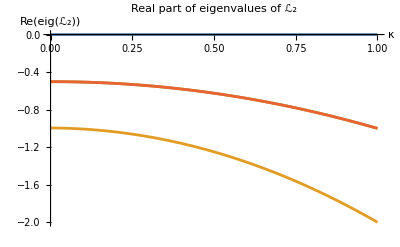

```mathematica
Simplify[Eigenvalues[Subscript[ℒ, 2]]]
Plot[Evaluate[Re[%/.{s->1,ϵ->0.2}]],{κ,0,1},AxesLabel->{κ,"Re(eig(ℒ_2))"},PlotLabel->"Real part of eigenvalues of ℒ_2"]
```

The following plot shows the real part of the eigenvalues of the superoperator ℒ_2, without Hamiltonian part. For small κ, there is still a sizable distance to eigenvalue 0.

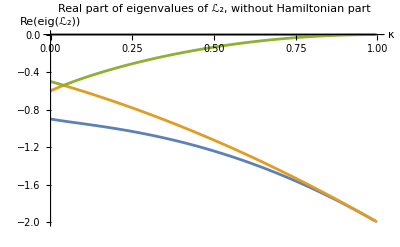

```mathematica
Simplify[Eigenvalues[Subscript[ℒ, 2]/.{s->0,ϵ->0.2}],Assumptions->{ϵ∈Reals,κ∈Reals}];
Plot[Evaluate[Re[%]],{κ,0,1},AxesLabel->{κ,"Re(eig(ℒ_2))"},PlotLabel->"Real part of eigenvalues of ℒ_2, without Hamiltonian part"]
```

```mathematica
Subscript[ρ, stat,2]=Block[{n=Simplify[NullSpace[Subscript[ℒ, 2]]]⟦1⟧},n=ArrayReshape[n,{2,2}];Simplify[n/Tr[n]]]
```

{{(16 s^2+(1+ϵ^2) (-1+κ^2)^2)/(16 s^2 (1+κ^2)+(-1+κ^2)^2 (1+2 ϵ^2+κ^2)),-(ϵ (-1+κ)^2 (1+κ) (-4 ⅈ s+(1+κ)^2))/(16 s^2 (1+κ^2)+(-1+κ^2)^2 (1+2 ϵ^2+κ^2))},{-(ϵ (-1+κ)^2 (1+κ) (4 ⅈ s+(1+κ)^2))/(16 s^2 (1+κ^2)+(-1+κ^2)^2 (1+2 ϵ^2+κ^2)),1/(1+(16 s^2+(1+ϵ^2) (-1+κ^2)^2)/(ϵ^2 (-1+κ^2)^2+κ^2 (16 s^2+(-1+κ^2)^2)))}}

```mathematica
Series[Subscript[ρ, stat,2],{ϵ,0,2},{κ,0,2}]
```

{{(1-κ^2+O[κ]^3)+(1/(-1-16 s^2)+((3+80 s^2) κ^2)/((1+16 s^2)^2)+O[κ]^3) ϵ^2+O[ϵ]^3,(ⅈ/(-ⅈ+4 s)-(ⅈ κ)/(ⅈ+4 s)-(ⅈ (-ⅈ+8 s) κ^2)/(-ⅈ+4 s)^2+O[κ]^3) ϵ+O[ϵ]^3},{(-ⅈ/(ⅈ+4 s)+(ⅈ κ)/(-ⅈ+4 s)+(ⅈ (ⅈ+8 s) κ^2)/(ⅈ+4 s)^2+O[κ]^3) ϵ+O[ϵ]^3,(κ^2+O[κ]^3)+(1/(1+16 s^2)+((-3-80 s^2) κ^2)/((1+16 s^2)^2)+O[κ]^3) ϵ^2+O[ϵ]^3}}

To second order in ϵ and κ, the stationary state is:

ρ_stat=(1 | 0
0 | 0)+ϵ(0 | -(1/(1+4ⅈ s)+κ 1/(1-4ⅈ s))
-(1/(1-4ⅈ s)+κ 1/(1+4ⅈ s)) | 0)-(ϵ^2/(1+(4s)^2)+κ^2)Z

Note that the ϵ^2-dependent diagonal terms and ϵ κ-dependent off-diagonal terms are suppressed by large s.

### System of dimension 3

By working in the eigenbasis of the Hamiltonian, we can assume that it has a diagonal matrix representation.

```mathematica
Subscript[H, 3]=DiagonalMatrix[{Subscript[λ, 1],Subscript[λ, 2],Subscript[λ, 3]}];
```

Admitting jumps to the same or higher energy levels with small rate ϵ and κ, respectively:

```mathematica
(* jump operator *)
Subscript[K, 3]={{ϵ,1,0},{κ,ϵ,1},{0,κ,ϵ}};
%//MatrixForm
```

(ϵ | 1 | 0
κ | ϵ | 1
0 | κ | ϵ)

Superoperator representation of Lindbladian, including Hamiltonian part:

```mathematica
Subscript[ℒ, 3]=Simplify[HamiltonianSuperoperator[Subscript[H, 3]]+LindbladOperatorMatrix[Subscript[K, 3]],Assumptions->{ϵ∈Reals,κ∈Reals}];
%//MatrixForm
```

(-κ^2 | 1/2 (ϵ-ϵ κ) | -κ/2 | 1/2 (ϵ-ϵ κ) | 1 | 0 | -κ/2 | 0 | 0
1/2 ϵ (-1+κ) | -1/2-κ^2-ⅈ λ_1+ⅈ λ_2 | 1/2 (ϵ-ϵ κ) | κ | 1/2 (ϵ-ϵ κ) | 1 | 0 | -κ/2 | 0
-κ/2 | 1/2 ϵ (-1+κ) | 1/2 (-1-κ^2-2 ⅈ λ_1+2 ⅈ λ_3) | 0 | κ | 1/2 (ϵ-ϵ κ) | 0 | 0 | -κ/2
1/2 ϵ (-1+κ) | κ | 0 | -1/2-κ^2+ⅈ λ_1-ⅈ λ_2 | 1/2 (ϵ-ϵ κ) | -κ/2 | 1/2 (ϵ-ϵ κ) | 1 | 0
κ^2 | 1/2 ϵ (-1+κ) | κ | 1/2 ϵ (-1+κ) | -1-κ^2 | 1/2 (ϵ-ϵ κ) | κ | 1/2 (ϵ-ϵ κ) | 1
0 | κ^2 | 1/2 ϵ (-1+κ) | -κ/2 | 1/2 ϵ (-1+κ) | -1-κ^2/2-ⅈ λ_2+ⅈ λ_3 | 0 | κ | 1/2 (ϵ-ϵ κ)
-κ/2 | 0 | 0 | 1/2 ϵ (-1+κ) | κ | 0 | 1/2 (-1-κ^2+2 ⅈ λ_1-2 ⅈ λ_3) | 1/2 (ϵ-ϵ κ) | -κ/2
0 | -κ/2 | 0 | κ^2 | 1/2 ϵ (-1+κ) | κ | 1/2 ϵ (-1+κ) | -1-κ^2/2+ⅈ λ_2-ⅈ λ_3 | 1/2 (ϵ-ϵ κ)
0 | 0 | -κ/2 | 0 | κ^2 | 1/2 ϵ (-1+κ) | -κ/2 | 1/2 ϵ (-1+κ) | -1)

First considering the idealized case when ϵ=0 and κ=0:

```mathematica
FullSimplify[Eigensystem[Subscript[ℒ, 3]/.{ϵ->0,κ->0}]]
MatrixForm[ArrayReshape[#,{3,3}]]&/@Last[%]
```

{{-1,-1,0,-1/2-ⅈ λ_1+ⅈ λ_2,-1/2+ⅈ λ_1-ⅈ λ_2,-1/2-ⅈ λ_1+ⅈ λ_3,-1/2+ⅈ λ_1-ⅈ λ_3,-1-ⅈ λ_2+ⅈ λ_3,ⅈ (ⅈ+λ_2-λ_3)},{{-1,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0},{0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0},{0,-(2 ⅈ)/(ⅈ+2 λ_1-4 λ_2+2 λ_3),0,0,0,1,0,0,0},{0,0,0,(2 ⅈ)/(-ⅈ+2 λ_1-4 λ_2+2 λ_3),0,0,0,1,0}}}

{(-1 | 0 | 0
0 | 1 | 0
0 | 0 | 0),(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0),(1 | 0 | 0
0 | 0 | 0
0 | 0 | 0),(0 | 1 | 0
0 | 0 | 0
0 | 0 | 0),(0 | 0 | 0
1 | 0 | 0
0 | 0 | 0),(0 | 0 | 1
0 | 0 | 0
0 | 0 | 0),(0 | 0 | 0
0 | 0 | 0
1 | 0 | 0),(0 | -(2 ⅈ)/(ⅈ+2 λ_1-4 λ_2+2 λ_3) | 0
0 | 0 | 1
0 | 0 | 0),(0 | 0 | 0
(2 ⅈ)/(-ⅈ+2 λ_1-4 λ_2+2 λ_3) | 0 | 0
0 | 1 | 0)}

The stationary state is ρ_stat=(1 | 0 | 0
0 | 0 | 0
0 | 0 | 0), as expected.

Real part of eigenvalues of superoperator ℒ_3:

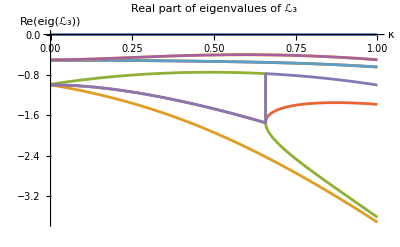

```mathematica
Simplify[Eigenvalues[Subscript[ℒ, 3]]];
Plot[Evaluate[Re[%/.{Subscript[λ, i_]:>i-1,ϵ->0.2}]],{κ,0,1},AxesLabel->{κ,"Re(eig(ℒ_3))"},PlotLabel->"Real part of eigenvalues of ℒ_3"]
```

The following plot shows the real part of the eigenvalues of the superoperator ℒ_3, without Hamiltonian part. For small κ, there is still a sizable distance to eigenvalue 0.

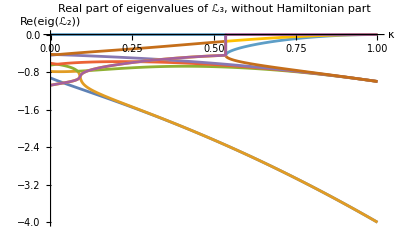

```mathematica
Simplify[Eigenvalues[Subscript[ℒ, 3]/.{Subscript[λ, _]->0,ϵ->0.2}],Assumptions->{ϵ∈Reals,κ∈Reals}];
Plot[Evaluate[Re[%]],{κ,0,1},AxesLabel->{κ,"Re(eig(ℒ_2))"},PlotLabel->"Real part of eigenvalues of ℒ_3, without Hamiltonian part"]
```

```mathematica
(* calling Simplify here takes very long *)
Subscript[ρ, stat,3]=Block[{n=NullSpace[Subscript[ℒ, 3]]⟦1⟧},n=ArrayReshape[n,{3,3}];n/Tr[n]];
```

```mathematica
FullSimplify[Series[Diagonal[Subscript[ρ, stat,3]],{ϵ,0,1},{κ,0,2}]]
```

{(1-κ^2+O[κ]^3)+O[ϵ]^2,((4 (λ_1-λ_3)^2 κ^2)/(1+4 (λ_1-λ_3)^2)+O[κ]^3)+O[ϵ]^2,(κ^2/(1+4 (λ_1-λ_3)^2)+O[κ]^3)+O[ϵ]^2}

```mathematica
(* special case κ=0 *)
Subscript[ρ, stat,3,κ0]=Block[{n=NullSpace[Subscript[ℒ, 3]/.{κ->0}]⟦1⟧},n=ArrayReshape[n,{3,3}];Simplify[n/Tr[n]]];
```

Note that ϵ is rescaled by the Hamiltonian eigenvalue difference:

```mathematica
FullSimplify[Series[Subscript[ρ, stat,3,κ0],{ϵ,0,2}]]
```

{{1+ϵ^2/(-1-4 (λ_1-λ_2)^2)+O[ϵ]^3,(ⅈ ϵ)/(-ⅈ+2 λ_1-2 λ_2)+O[ϵ]^3,ϵ^2/((ⅈ-2 λ_1+2 λ_2) (-ⅈ+2 λ_1-2 λ_3))+O[ϵ]^3},{-(ⅈ ϵ)/(ⅈ+2 λ_1-2 λ_2)+O[ϵ]^3,ϵ^2/(1+4 (λ_1-λ_2)^2)+O[ϵ]^3,O[ϵ]^3},{ϵ^2/((-ⅈ-2 λ_1+2 λ_2) (ⅈ+2 λ_1-2 λ_3))+O[ϵ]^3,O[ϵ]^3,O[ϵ]^4}}

```mathematica
(* special case ϵ=0 *)
Subscript[ρ, stat,3,ϵ0]=Block[{n=NullSpace[Subscript[ℒ, 3]/.{ϵ->0}]⟦1⟧},n=ArrayReshape[n,{3,3}];Simplify[n/Tr[n]]];
```

The first-order κ dependence (for ϵ=0) is also rescaled by the Hamiltonian eigenvalue difference:

```mathematica
FullSimplify[Series[Subscript[ρ, stat,3,ϵ0],{κ,0,2}]]
```

{{1-κ^2+O[κ]^3,0,(ⅈ κ)/(-ⅈ+2 λ_1-2 λ_3)+O[κ]^3},{0,(4 (λ_1-λ_3)^2 κ^2)/(1+4 (λ_1-λ_3)^2)+O[κ]^3,0},{-(ⅈ κ)/(ⅈ+2 λ_1-2 λ_3)+O[κ]^3,0,κ^2/(1+4 (λ_1-λ_3)^2)+O[κ]^3}}